```mathematica
fYX[x_,y_]:= 4(x-y)^3/x^4
fX[x_]:=4x^3Exp[-x^4/theta^4]/theta^4

Integrate[fX[x]*x,{x,0,Infinity}]
Integrate[fX[x]*x^2,{x,0,Infinity}]
Integrate[fX[x]*x^3,{x,0,Infinity}]

Integrate[fYX[x,y]*fX[x],{x,y,Infinity}]
```

ConditionalExpression[Gamma[5/4]/((1/theta^4)^(1/4)), Re[theta^4]>0]

ConditionalExpression[(√π)/(2 √(1/theta^4)), Re[theta^4]>0]

ConditionalExpression[Gamma[7/4]/((1/theta^4)^(3/4)), Re[theta^4]>0]

ConditionalExpression[(4 (-(9 √π y)/(√(1/theta^4))-40 ⅇ^(-y^4/theta^4) y^3+(9 √π y Erf[√(1/theta^4) y^2])/(√(1/theta^4))-3 y^3 Gamma[0,y^4/theta^4]+(36 y^2 Gamma[5/4,y^4/theta^4])/((1/theta^4)^(1/4))+(4 Gamma[7/4,y^4/theta^4])/((1/theta^4)^(3/4))))/(3 theta^4), Re[y]>0&&Im[y]==0&&Re[theta^4]>0]

```mathematica
Simplify[1/(3 theta^4)4 (-(9 √π y)/(√(1/theta^4))-40 ⅇ^(-y^4/theta^4) y^3+(9 √π y Erf[√(1/theta^4) y^2])/(√(1/theta^4))-3 y^3 Gamma[0,y^4/theta^4]+(36 y^2 Gamma[5/4,y^4/theta^4])/((1/theta^4)^(1/4))+(4 Gamma[7/4,y^4/theta^4])/((1/theta^4)^(3/4)))]
```

1/(3 theta^4)4 (-(9 √π y)/(√(1/theta^4))-40 ⅇ^(-y^4/theta^4) y^3+(9 √π y Erf[√(1/theta^4) y^2])/(√(1/theta^4))-3 y^3 Gamma[0,y^4/theta^4]+(36 y^2 Gamma[5/4,y^4/theta^4])/((1/theta^4)^(1/4))+(4 Gamma[7/4,y^4/theta^4])/((1/theta^4)^(3/4)))

1

1/5 Gamma[5/4]

(√π)/30

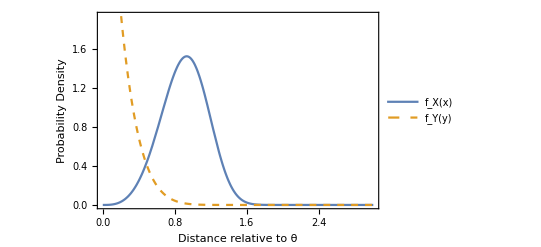

```mathematica
fY[y_]:=1/(3 theta^4)4 (-(9 √π y)/(√(1/theta^4))-40 ⅇ^(-y^4/theta^4) y^3+(9 √π y Erf[√(1/theta^4) y^2])/(√(1/theta^4))-3 y^3 Gamma[0,y^4/theta^4]+(36 y^2 Gamma[5/4,y^4/theta^4])/((1/theta^4)^(1/4))+(4 Gamma[7/4,y^4/theta^4])/((1/theta^4)^(3/4)))



theta=1
Integrate[fY[y]*y,{y,0,Infinity}]
Integrate[fY[y]*y^2,{y,0,Infinity}]


Plot[{fX[x], fY[x]},{x,0,3}, PlotStyle-> {Line, Dashed}, Frame-> True, FrameLabel-> {Style["Distance relative to θ", Bold, 12],Style["Probability Density", Bold, 12] }, RotateLabel->True, PlotLegends-> Placed[{"f_X(x)", "f_Y(y)"},{0.85,0.8}]]
```